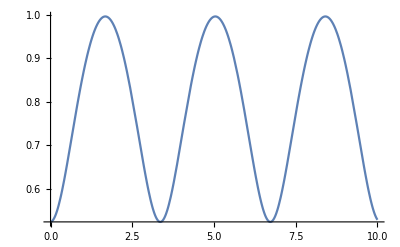

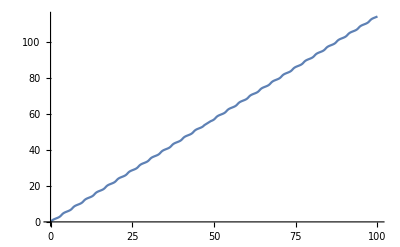

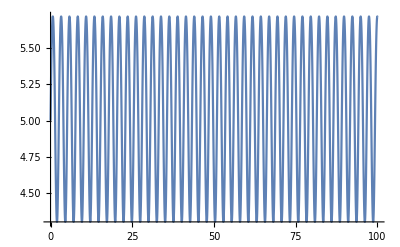

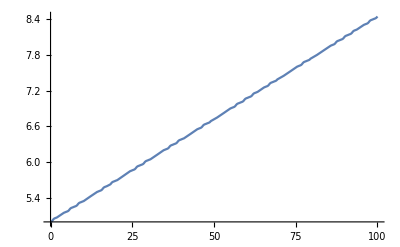

```mathematica
g=10;
l=10;
m = 1;
L = 50;

θ0 = Pi/6;
dθ0 = 1/100;
ϕ0 = 0;

a=NDSolve[{θ''[t] + (g/l)Sin[θ[t]]-((ϕ'[t])^2)Cos[θ[t]]*Sin[θ[t]]==0, θ[0] == θ0, θ'[0]== dθ0, m*l^2*ϕ'[t]*(Sin[θ[t]])^2 == L, ϕ[0] == ϕ0}, {θ,ϕ},{t, 0, 100}];
θt[t_] = θ[t]/.Flatten[a];
ϕt[t_] = ϕ[t]/.Flatten[a];

Animate[trail = Table[{l*Sin[θt[tt]]*Cos[ϕt[tt]], l*Sin[θt[tt]]*Sin[ϕt[tt]], -l*Cos[θt[tt]]}, {tt, 0, t, 0.1}];Graphics3D[{Red, Point[trail],Black, Line[{{0,0,0},{l*Sin[θt[t]]*Cos[ϕt[t]], l*Sin[θt[t]]*Sin[ϕt[t]], -l*Cos[θt[t]]}}],Blue,Sphere[{l*Sin[θt[t]]*Cos[ϕt[t]], l*Sin[θt[t]]*Sin[ϕt[t]], -l*Cos[θt[t]]}], Black,Ellipsoid[{l*Sin[θt[t]]*Cos[ϕt[t]], l*Sin[θt[t]]*Sin[ϕt[t]], -15}, {1,1,.01}]},  PlotRange->{{-10., 10.}, {-10.,  10.}, {-15., 2.}}], {t, 0, 10}]

Plot[Evaluate[θ[t]/.a],{t,0,10},PlotRange-> All]
Plot[Evaluate[ϕ[t]/.a],{t,0,100},PlotRange-> All]
```